# Complex Visualization

## Basic Built In Complex Plot

We want to to plot complex functions f:ℂ→ℂ.  This is more complicated than you might guess because a complex function of a complex arguments generates two functions
	fr[x,y]=Re[f[x+ I y]]
and 
	fi[x,y]=Im[f[x+ I y]]
of  two real variables.  Instead of splitting things up into real and imaginary (which is a Cartesian way of thinking about things) it is more common to split things up using polar coordinates into size and angle. 
	x+ⅈ y=r ⅇ^(ⅈ θ)
or if you want
	x=r Cos[θ] and y=r Sin[θ]
or the other way around
	r=√(x^2+y^2) and θ=ArcTan[x,y].
The Mathematica command for magnitude is “Abs”. The Mathematica command for argument is “Arg”.

```mathematica
{x,y}={1.2,-1.3};
z=x+ ⅈ y
Abs[z] ⅇ^(ⅈ Arg[z])
Abs[z]E^(Arg[z] I)
```

1.2-1.3 ⅈ

1.2-1.3 ⅈ

1.2-1.3 ⅈ

We can now start to understand pretty pictures of complex functions.

```mathematica
f[z_]:=z
TabView[{
"3D"->ComplexPlot3D[f[z],{z,3},PlotLegends->Automatic,Mesh->Automatic],
"Flat"->ComplexPlot[f[z],{z,3},PlotLegends->Automatic,Mesh->Automatic]}]
```

12

Lets make some more.

```mathematica
f[z_]:=z^2
ComplexPlot3D[f[z],{z,3},PlotLegends->Automatic,Mesh->Automatic]
```

-Graphics3D-

```mathematica
f[z_]:=Sin[z]
ComplexPlot3D[f[z],{z,3},PlotLegends->Automatic,Mesh->Automatic]
```

-Graphics3D-

```mathematica
f[z_]:=Sin[z]
ComplexPlot3D[f[z^2],{z,1},PlotLegends->Automatic,Mesh->Automatic]
```

-Graphics3D-

```mathematica
f[z_]:=1/z
ComplexPlot3D[f[z],{z,3},PlotLegends->Automatic,Mesh->Automatic]
```

-Graphics3D-

```mathematica
f[z_]:=1/z^2
TabView[{
"3D"->ComplexPlot3D[f[z],{z,3},PlotLegends->Automatic,Mesh->Automatic],
"Flat"->ComplexPlot[f[z],{z,3},PlotLegends->Automatic,Mesh->Automatic]}]
```

12

## Poles and Zeros

A point z_0∈ℂ is a zero of a function f if f[z_0]=0.

A point z_0∈ℂ is a pole of a function f if it is a zero of 1/f.

Lets look at a slightly more interesting function!  I need to mess with the vertical range a bit. Can we eyeball poles and zeros? How many of each should there be?

```mathematica
f[z_]:=(1+1.2 z^2-2.3 z^3+z^4)/(z+2.3 z^7)
TabView[{
"f"->ComplexPlot3D[f[z],{z,2},PlotLegends->Automatic,Mesh->Automatic,PlotRange->{0,10}],
"1/f"->ComplexPlot3D[1/f[z],{z,2},PlotLegends->Automatic,Mesh->Automatic,
PlotPoints->100]
}]
```

12

The function below is NOT the same as the one above.

```mathematica
f[z_]:=(1+1.2 z^2-2.3 z^3+z^4)/(z^2+2.3 z^7)
TabView[{
"f"->ComplexPlot3D[f[z],{z,2},PlotLegends->Automatic,Mesh->Automatic,
PlotRange->{0,10}],
"1/f"->ComplexPlot3D[1/f[z],{z,2},PlotLegends->Automatic,Mesh->Automatic]
}]
```

12

## √z and other things have Cuts

Why should the √z be different?

```mathematica
f[z_]:=√z
TabView[{
"f"->ComplexPlot3D[f[z],{z,2},PlotLegends->Automatic,Mesh->Automatic],
"1/f"->ComplexPlot3D[1/f[z],{z,2},PlotLegends->Automatic,Mesh->Automatic]
}]
```

12

Conventionally people write f(z)=u(x,y)+ⅈ v(x,y) where z=x+ ⅈ y and u(x,y) is the real part of f and v is the imaginary part of f.

The difference is obvious if we look at the real and imaginary parts separately.

```mathematica
f[z_]:=√z
Plot3D[{Re[f[x+I y]],Im[f[x+ I y]]},{x,-2,2},{y,-2,2},
PlotLegends->{"re","im"},
PlotLabel->f[z]]
```

-Graphics3D-

One way to think about this becomes clearer in polar coordinates.
	√(r ⅇ^(ⅈ θ))=√r ⅇ^(ⅈ θ/2)=√r(cos(θ/2)+ⅈ sin(θ/2))

```mathematica
g[r_,θ_]:=√r(Cos[θ/2]+ⅈ Sin[θ/2])
TabView[{
"Half"->ParametricPlot3D[{
{r Cos[θ],r Sin[θ],Re[g[r,θ]]},
{r Cos[θ],r Sin[θ],Im[g[r,θ]]}},{r, 0,2},{θ,0,2π}],
"Whole"->ParametricPlot3D[{
{r Cos[θ],r Sin[θ],Re[g[r,θ]]},
{r Cos[θ],r Sin[θ],Im[g[r,θ]]}},{r, 0,2},{θ,0,4π}]}]
```

12

## More Pictures

```mathematica
f[z_]:= Log[1+z];
TabView[{
"C Plot"->ComplexPlot3D[f[z],{z,-2-2I,2+2I},
PlotLegends->Automatic,
Mesh->Automatic],
"ReIm Plot"->Plot3D[{Re[f[x+I y]],Im[f[x+I y]]},{x,-2,2},{y,-2,2},
PlotLegends->{"re","im"},
Mesh->Automatic]
}]
```

12

```mathematica
f[z_]:= Sin[z];
TabView[{
"C Plot"->ComplexPlot3D[f[z],{z,-5-2I,5+2I},
PlotLegends->Automatic,
Mesh->Automatic],
"ReIm Plot"->Plot3D[{Re[f[x+I y]],Im[f[x+I y]]},{x,-5,5},{y,-2,2},
PlotLegends->{"re","im"},
Mesh->Automatic]
}]
```

12

```mathematica
f[z_]:= √((1-z)(1+z));
TabView[{
"C Plot"->ComplexPlot3D[f[z],{z,-2-2I,2+2I},
PlotLegends->Automatic,
Mesh->Automatic],
"ReIm Plot"->Plot3D[{Re[f[x+I y]],Im[f[x+I y]]},{x,-2,2},{y,-2,2},
PlotLegends->{"re","im"},
Mesh->Automatic]
}]
```

12

This one probably needs some thinking.

```mathematica
f[z_]:= Exp[1/z];
R=2;
TabView[{
"C Plot"->ComplexPlot3D[f[z],{z,-R(1+I),R(1+I)},
PlotLegends->Automatic,
Mesh->Automatic],
"ReIm Plot"->Plot3D[{Re[f[x+I y]],Im[f[x+I y]]},{x,-R,R},{y,-R,R},
PlotLegends->{"re","im"},
Mesh->Automatic]
}]
```

12

```mathematica
f[z_]:= Exp[1/z];
R=.1;
TabView[{
"C Plot"->ComplexPlot3D[f[z],{z,-R(1+I),R(1+I)},
PlotLegends->Automatic,
PlotPoints->100,
Mesh->None],
"ReIm Plot"->Plot3D[{Re[f[x+I y]],Im[f[x+I y]]},{x,-R,R},{y,-R,R},
PlotLegends->{"re","im"},
Mesh->Automatic]
}]
```

12

## Riemann Sphere

The Riemann Sphere is a way to make a picture of ℂ with a single point added at ∞.  All you do is stick a sphere radius 1 centered at {0,0,1} right above the origin of ℂ at 0+0ⅈ and draw a line from any point in ℂ to the North pole {0,0,2}. Th point in ℂ maps to the point on the sphere where the line intersects the sphere.    Here is a simple pic I made.

```mathematica
Pic=ParametricPlot3D[ {
{-Cos[θ]Cot[ϕ],-Sin[θ]Cot[ϕ],0} ,
{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]+1}
},{θ,0, 2π},{ϕ,-π,π},
PlotStyle->{Opacity[0.5],Opacity[0.5]}];
Manipulate[Show[Pic,
Graphics3D[{Red, Thickness[0.02],Line[{{0,0,2},r{Cos[θ],Sin[θ],0}}]}]],
{{r,1},0,10},
{θ,0, 2π}]
```

Show::gcomb: Could not combine the graphics objects in Show[Pic, -Graphics3D-]
    .

Show::gcomb: Could not combine the graphics objects in Show[Pic,].

Here is a fancy pic that Christopher Grattoni made. https://demonstrations.wolfram.com/TheRiemannSphereAsAStereographicProjection/

If you think about this it is one way to start making sense out of our pictures for ⅇ^(1/z).

## Branch Cut Matters or maybe Branch Cuts Matter

We plotted √(1-z^2) earlier.  Somehow we think we should have 
	√(1-z^2)=√((-1)(z^2-1))=√-1 √(z^2-1)=ⅈ √(z^2-1).
We need to understand why the pics below are not the same.

```mathematica
f1[z_]:=√(1-z^2)
f2[z_]:=ⅈ √(z^2-1)
TabView[{
"f1"->ComplexPlot3D[f1[z],{z,2},Mesh->Automatic,PlotLegends->Automatic],
"f2"->ComplexPlot3D[f2[z],{z,2},Mesh->Automatic,PlotLegends->Automatic]
}]
TabView[{
"f1"->Plot3D[{Re[f1[x+ⅈ y]],Im[f1[x+ⅈ y]]},
{x,-2,2},{y,-2,2},Mesh->Automatic,PlotLegends->{"re","im"}],
"f2"->Plot3D[{Re[f2[x+ⅈ y]],Im[f2[x+ⅈ y]]},
{x,-2,2},{y,-2,2},Mesh->Automatic,PlotLegends->{"re","im"}]
}]
```

12

12

We need to think about the best ways to choose branch cuts!

## Analytic Continuation

Analytic functions can be represented locally by convergent Taylor Series.  We saw how to make a chain of Taylor Series to sneak around some singularities in the complex plane.

```mathematica
n=10;
f[z_]:= ArcTan[z];
z1=1.0;
f1[z_]= Normal[Series[f[z],{z,z1,n}]];
z2=1.5+ⅈ;
f2[z_]= Normal[Series[f[z],{z,z2,n}]];
z3=1.5+2ⅈ;
f3[z_]= Normal[Series[f[z],{z,z3,n}]];
z4=0.5+3ⅈ;
f4[z_]= Normal[Series[f[z],{z,z4,n}]];
Show[
ComplexPlot3D[ f[z],{z,3},PlotLegends->Automatic],
ComplexPlot3D[ f1[z],{z,z1-(1+I),z1+(1+ⅈ)},
RegionFunction:>Function[z,Abs[z-z1]<1],
Mesh->Automatic,
MeshStyle->Red],
ComplexPlot3D[ f2[z],{z,z2-(1+ⅈ),z2+(1+ⅈ)},
RegionFunction:>Function[z,Abs[z-z2]<1],
Mesh->Automatic,
MeshStyle->Blue],
ComplexPlot3D[ f3[z],{z,z3-(1+ⅈ),z3+(1+ⅈ)},
RegionFunction:>Function[z,Abs[z-z3]<1],
Mesh->Automatic,
MeshStyle->Green],
ComplexPlot3D[ f4[z],{z,z4-(1+ⅈ),z4+(1+ⅈ)},
RegionFunction:>Function[z,Abs[z-z4]<1],
Mesh->Automatic,
MeshStyle->Cyan]
]
```

-Graphics3D-

## Conformal Mapping

A conformal mapping preserves local angles. Many complex functions give conformal mappings

```mathematica
Manipulate[
ParametricPlot[{ReIm[x+ⅈ y],ReIm[r ⅇ^(ⅈ θ)(x+I y)]},{x,-2,2},{y,-2,2},
Mesh->All,
PlotLabel->r ⅇ^(ⅈ θ),
PlotRange->{{-3,3},{-3,3}}],
{{r,1}, 0, 2},
{{θ,0.1},0, 2π}]
```

```mathematica
Solve[z==t/(1+t),t]
```

{{t→-z/(-1+z)}}

-z/(-1+z)

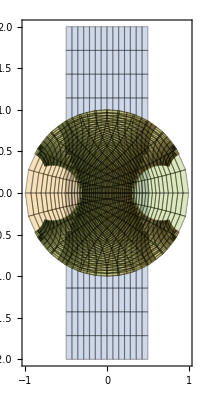

```mathematica
f[z_]=z/(1+z);
fInv[z_]=-z/(z-1)
ParametricPlot[{ReIm[x+ⅈ y],ReIm[f[x+I y]],ReIm[fInv[x+I y]]},{x,-0.5,0.5},{y,-2,2},
Mesh->All,
PlotRange->All]
```